# Optimizing population bottlenecks

Define variables:

```mathematica
d = Symbol["d"]; (*dilution ratio*)
r=Symbol["r"]; (*growth rate*)
t=Symbol["t"]; (*time at which mutation occurs*)
s=Symbol["s"]; (*selective benefit of mutation*)
```

Create some useful helper expressions to simplify the notation:

```mathematica
tau = - Log[d]/r; (*length of growth period*)
b=Exp[-r*(tau-t)*(1+s)]; (*inverse of expected number of mutants at the end of the growth period*)
g=(1-b)*(1-d);
```

Calculate the probability of i mutants remaining after the bottleneck. We need to define i=0 separately.

```mathematica
P[i_]=b(1-d)(d/(1-d))^i * Sum[g^(j-1)*Binomial[j,i],{j,i,Infinity}];
p0 = b (1-d) Sum[g^(j-1)*Binomial[j,0],{j,1,Infinity}];
```

Define v0s as the nontrivial solution to the infinite sum equation

```mathematica
solution = Solve[v0s==p0+Sum[P[i]*v0s^i,{i,1,Infinity}]/.t->0,v0s];
v0s=v0s/. Select[solution,#=!={v0s->1}&][[1]]
```

((-1+d) d^s)/(-1+d^(1+s))

Using v0s, find the chance of extinction for any t and s, V(t,s). We did not display this in the main text because the solution is so unwieldy.

```mathematica
v = p0+Sum[P[i]*v0s^i,{i,1,Infinity}]
```

-((-1+d) d^(-1+s) ⅇ^(-r (1+s) (-t-Log[d]/r)))/((-1-d^s ⅇ^(r t+r s t)+d^(1+s) ⅇ^(r t+r s t)) (-1+d^s-d^s ⅇ^(r t+r s t)+d^(1+s) ⅇ^(r t+r s t)))-((-1+d) ⅇ^(-r (1+s) (-t-Log[d]/r)) (-1+ⅇ^(r (1+s) (-t-Log[d]/r))))/((1-ⅇ^(-r (1+s) (-t-Log[d]/r))) (1-d+d ⅇ^(r (1+s) (-t-Log[d]/r))))

Find the rate of mutations occurring at time t and selective benefit s that will eventually fix (we ignore the population size and mutation rate here, the fixation rate is simply proportional to their product).

```mathematica
integrand = Simplify[d r Exp[r t](1-v)/tau]
```

-(d (-1+d^s) ⅇ^(r t) r^2)/((-1+d^(1+s) ⅇ^(r (1+s) t)-d^s (-1+ⅇ^(r (1+s) t))) Log[d])

Find the expected number of mutants that will occur and go onto fix in one growth period, conditional on them having selective benefit s.

```mathematica
gamma=Integrate[integrand,{t,0,tau},Assumptions->{r>0,d>0,d<1,t>0,s>0}]
```

-1/Log[d]r (Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]-d Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)])

Note that there is no exact closed form integral available over values of s.

```mathematica
Integrate[gamma*a*Exp[-a*s],{s,0,Infinity}]
```

∫_0^∞ -1/Log[d]a ⅇ^(-a s) r (Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]-d Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)])ⅆs

Check how good the approximations are

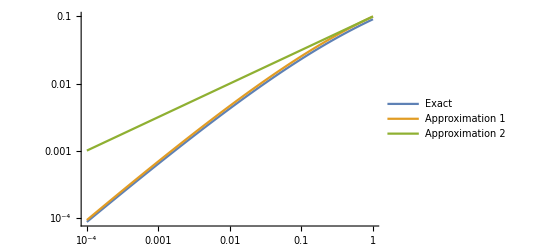

```mathematica
LogLogPlot[Evaluate[{gamma,r s Log[1/d]/(1/d-1), r s Sqrt[d] }/. {r->1,s->0.1}],{d,0.0001,1}, PlotLegends->{"Exact","Approximation 1","Approximation 2"}]
```

Check the rate of mutations that go onto fix at different times t within one growth period. Note the y axis.

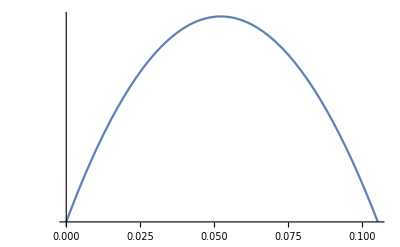

```mathematica
LogPlot[Evaluate[integrand/. {r->1,s->0.1,d->0.9001}],{t,0,tau/.{r->1,d->0.9001}}]
```